# Cálculo de las secciones transversales de absorción, esparcimiento y extinción

```mathematica
Needs["MaTeX`"]
```

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
vlight=3*^17 ;(*nm s^-1*)
ϵ0=8.854187812*10^(-3)(*F/nm*);
```

Definiendo los factores de depolarización considerando los casos para un elipsoide oblato (a=b) L1= L2 y uno prolato (b=c) L2=L3

```mathematica
elipsoblato[a_,b_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1,L2,L3},
							L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L2=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L3=1-2 L1;
{L1,L2,L3}]
```

```mathematica
elipsprolato[a_,b_,c_]:=Module[{eab2=1-(b^2/a^2),L1,L2,L3},
							L1=((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])]);
							L2=0.5*(1-L1);
							L3=0.5*(1-L1);{L1,L2,L3}];
```

```mathematica
factgeom[j_,a_,b_,c_]:=Which[a==b==c,1/3,a==b ,elipsoblato[a,b,c][[j]],
							b==c ,elipsprolato[a,b,c][[j]]]
```

```mathematica
factgeom[1,30.2,10,10]
```

0.107827

```mathematica
(*COMPROBANDO FUNCIONAMIENTO DE LOS FACTORES PARA OBLATO Y PROLATO*)
```

```mathematica
L1[a_,b_]:=Module[{eab2=1-(b^2/a^2),L1},L1=((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])])]
L11[a_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1},L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2)]
```

```mathematica
hola=Table[{Sqrt[1-(c^2/10^2)],L11[10,c]},{c,0.001,10,0.01}];
hola2=Table[{Sqrt[1-(b^2/10^2)],L1[10,b]},{b,0.001,10,0.01}];
```

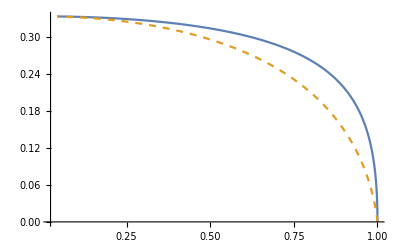

```mathematica
ListLinePlot[{hola,Style[hola2,Dashed]},PlotRange->All]
```

## Definiciones

### Función dieléctrica de tipo Drude

Definiendo la sección transversal de absorción

```mathematica
Cabs[a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,αx,αz,Cabs,Cabsx,Cabsz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Cabs=k Im[2 αx+αz]/3;
										Cabsx=k Im[αx];
										Cabsz=k Im[αz];
										{Cabs,Cabsx,Cabsz}]
```

```mathematica
Csca[a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,αx,αz,Csca,Cscax,Cscaz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Csca=k^4 Norm[2 αx+αz]^2/(18 Pi);
										Cscax=k^4 Norm[αx]^2/(6 Pi);
										Cscaz=k^4 Norm[αx]^2/(6 Pi);
										{Csca,Cscax,Cscaz}]
```

```mathematica
Cext[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[1]]+Cabs[a,b,c,nm,λ,λp,γ][[1]]
Cextx[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[2]]+Cabs[a,b,c,nm,λ,λp,γ][[2]]
Cextz[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[3]]+Cabs[a,b,c,nm,λ,λp,γ][[3]]
```

### Datos experimentales

```mathematica
Cabsexp[a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,αx,αz,Cabs,Cabsx,Cabsz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Cabs=k Im[2αx+ αz]/3;
										Cabsx=k Im[αx];
										Cabsz=k Im[αz];
										{Cabs,Cabsx,Cabsz}]
```

```mathematica
Cscaexp[a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,αx,αz,Csca,Cscax,Cscaz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Csca=k^4 Norm[2 αx+ αz]^2/(18 Pi);
										Cscax=k^4 Norm[αx]^2/(6 Pi);
										Cscaz=k^4 Norm[αz]^2/(6Pi);
										{Csca,Cscax,Cscaz}]
```

```mathematica
Cextexp[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[1]]+Cabsexp[a,b,c,nm,λ,np][[1]]
Cextexpx[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[2]]+Cabsexp[a,b,c,nm,λ,np][[2]]
Cextexpz[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[3]]+Cabsexp[a,b,c,nm,λ,np][[3]]
```

```mathematica
Cextexp[30,10,10,1.33,144,1]
```

66.7352

## Cálculos

### Datos experimentales

#### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]]*1000;
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
aluminio=Transpose[{λalum,naluminio}];
```

```mathematica
nindexalum=Interpolation[aluminio]
```

InterpolatingFunction[…]

```mathematica
h vlight/300
```

4.13567

Se graficará la Cext promedio contrastada con las Cext individuales

```mathematica
qextAlDrpromedio=Table[{h vlight/λ,Cext[2,2,1,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.01}];
qextAlDrx=Table[{h vlight/λ,Cextx[2,2,1,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.01}];
qextAlDrz=Table[{h vlight/λ,Cextz[2,2,1,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.01}];
```

```mathematica
upperTicksCext=Module[{labels,positions},labels={100,150,200,250};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorCext=Module[{labels,positions,size},labels={3.5,4.2,4.6,6,8,9,12,40};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

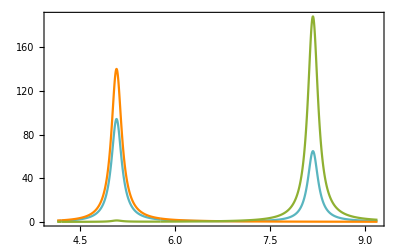

```mathematica
cextAl=ListLinePlot[{Style[qextAlDrpromedio,RGBColor[0.349,0.71,0.749]],Style[qextAlDrx,RGBColor[1,0.533,0]],Style[qextAlDrz]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [nm^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega"],Magnification->1.5],None}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorCext,upperTicksCext]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["\langle C_{ext} \langle"],MaTeX["C_{ext}^{(1)}"],MaTeX["C_{ext}^{(3)}"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}]]
```

```mathematica
Export["CextAl.pdf",cextAl]
```

CextAl.pdf

#### Elipsoide oblato

#### Cambiando el tamaño de a

```mathematica
qextAlDr=Table[{λ,Cext[1.5,1.5,1,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,70,350}];
qextAl1Dr=Table[{λ,Cext[1.75,1.75,1,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,70,350}];
qextAl2Dr=Table[{λ,Cext[2,2,1,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,70,350}];
qextAl3Dr=Table[{λ,Cext[2.5,2.5,1,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,70,350}];qextEsferaDr=Table[{λ,Cext[2,2,2,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,70,350}];
```

```mathematica
upperTicksAl=Module[{labels,positions},labels={3.6,4,5,7,10,15,25,60};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAl=Module[{labels,positions,size},labels={3.5,4.2,4.6,6,8,9,12,40};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

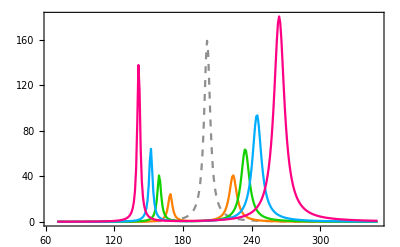

```mathematica
alc=ListLinePlot[{Style[qextEsferaDr,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAlDr,RGBColor[1,0.502,0]],Style[qextAl1Dr,RGBColor[0.071,0.82,0]],Style[qextAl2Dr,RGBColor[0,0.678,1]],Style[qextAl3Dr,RGBColor[1,0,0.518]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [nm^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega"],Magnification->1.5],None}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorCext,upperTicksCext]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["AR=1"],MaTeX["AR=1.5"],MaTeX["AR=1.75"],MaTeX["AR=2"],MaTeX["AR=2.5"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}]]
```

```mathematica
(*Export["Alc.pdf",alc]
```

Alc.pdf

#### Misma razón de aspecto

```mathematica
qextAlAR=Table[{λ,Cext[1,1,0.5,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,70,350}];
qextAl1AR=Table[{λ,Cext[2,2,1,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,70,350}];
qextAl2AR=Table[{λ,Cext[3,3,1.5,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,70,350}];
qextAl3AR=Table[{λ,Cext[4,4,2,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,70,350}];
```

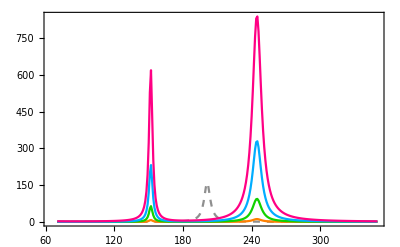

```mathematica
alAR=ListLinePlot[{Style[qextEsferaDr,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAlAR,RGBColor[1,0.502,0]],Style[qextAl1AR,RGBColor[0.071,0.82,0]],Style[qextAl2AR,RGBColor[0,0.678,1]],Style[qextAl3AR,RGBColor[1,0,0.518]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [nm^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega"],Magnification->1.5],None}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorCext,upperTicksCext]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["AR=1"],MaTeX["AR=1.5"],MaTeX["AR=1.75"],MaTeX["AR=2"],MaTeX["AR=2.5"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}]]
```

```mathematica
(*Export["AlAR.pdf",alAR]
```

AlAR.pdf

#### Para ver las contribuciones cambiando a

```mathematica
qabsAlcont=Table[{λ,Cabsexp[1,1,1,1.33,λ,nindexalum[λ]][[1]]},{λ,70,400}];
qscaAlcont=Table[{λ,Cscaexp[1,1,1,1.33,λ,nindexalum[λ]][[1]]},{λ,70,400}];
qextAlcont=Table[{λ,Cextexp[1,1,1,1.33,λ,nindexalum[λ]]},{λ,70,400}];
```

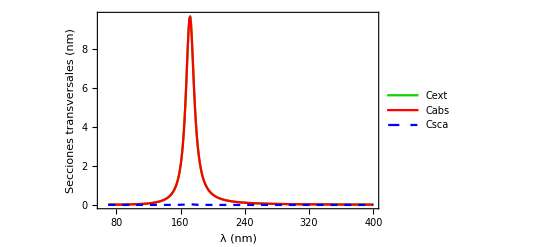

```mathematica
alcont=ListLinePlot[{Style[qextAlcont,RGBColor[0.071,0.82,0]],Style[qabsAlcont,Red],Style[qscaAlcont,Blue, Dashed]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAl,upperTicksAl]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
Export["AlContribuciones3.pdf",alcont]
```

AlContribuciones3.pdf

### Oro

Datos obtenidos de Johnson & Christy  DOI: https://doi.org/10.1103/PhysRevB.6.4370

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau11=Drop[Drop[au,{51,101}],1];
kau11=Drop[au,{1,52}];
λAu1=nau11[[All,1]]*1000; (*λ en nm*)
nau1=nau11[[All,2]];
kAu1=kau11[[All,2]];
nAu1=nau1+ I kAu1;
aU1=Transpose[{λAu1,nAu1}];
```

```mathematica
nindexau1=Interpolation[aU1];
```

```mathematica
300/(2*Pi*1.33)
```

35.8996

#### Elipsoide oblato

#### Cambiando el tamaño de a

```mathematica
qabsAuc=Table[{λ,Cabsexp[2,2,1,1.33,λ,nindexau1[λ]][[1]]},{λ,400,800}];
qscaAuc=Table[{λ,Cscaexp[2,2,1,1.33,λ,nindexau1[λ]][[1]]},{λ,400,800}];
qextAuc=Table[{λ,Cextexp[1,1,1,1.33,λ,nindexau1[λ]]},{λ,400,800}];
qextAu1c=Table[{λ,Cextexp[1,1,1,1.33,λ,nindexau1[λ]]},{λ,400,800}];
qextAu2c=Table[{λ,Cextexp[3.5,3.5,1,1.33,λ,nindexau1[λ]]},{λ,400,800}];
qextAu3c=Table[{λ,Cextexp[4,4,1,1.33,λ,nindexau1[λ]]},{λ,400,800}];
qextAuEsferac=Table[{λ,Cextexp[1,1,1,1.33,λ,nindexau1[λ]]},{λ,400,800}];
λtendencyAuc=Table[{522,C},{C,0,145}];
```

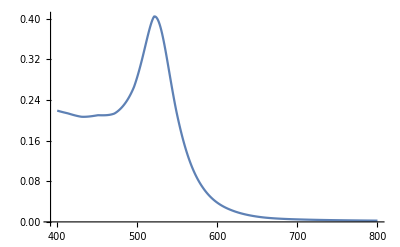

```mathematica
ListLinePlot[{qextAu1c}]
```

```mathematica
upperTicks4=Module[{labels,positions},labels={1.6,1.8,2,2.5,3,4};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={1.7,1.8,2.3,2.5,2.7,3.5,3.8};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

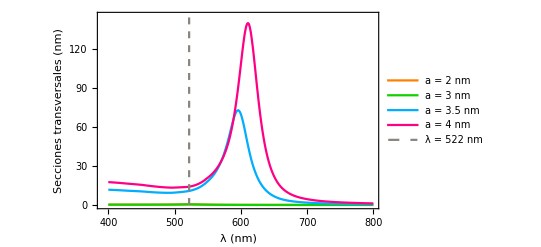

```mathematica
au1c=ListLinePlot[{Style[qextAuc,RGBColor[1,0.502,0]],Style[qextAu1c,RGBColor[0.071,0.82,0]],Style[qextAu2c,RGBColor[0,0.678,1]],Style[qextAu3c,RGBColor[1,0,0.518]],Style[λtendencyAuc,Dashed,RGBColor[0.541,0.518,0.498]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"a = 2 nm","a = 3 nm","a = 3.5 nm","a = 4 nm", "λ = 522 nm"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.65}]]
```

```mathematica
Export["Auc.pdf",au1c]
```

Auc.pdf

#### Misma razón de aspecto

```mathematica
qextAuAR=Table[{λ,Cextexp[1,1,0.5,1.33,λ,nindexau1[λ]]},{λ,300,800}];
qextAu1AR=Table[{λ,Cextexp[2,2,1,1.33,λ,nindexau1[λ]]},{λ,300,800}];
qextAu2AR=Table[{λ,Cextexp[3,3,1.5,1.33,λ,nindexau1[λ]]},{λ,300,800}];
qextAu3AR=Table[{λ,Cextexp[4,4,2,1.33,λ,nindexau1[λ]]},{λ,300,800}];
qextAuEsferaAR=Table[{λ,Cextexp[4,4,4,1.33,λ,nindexau1[λ]]},{λ,300,800}];
λtendencyAuAR=Table[{522,C},{C,0,45}];
```

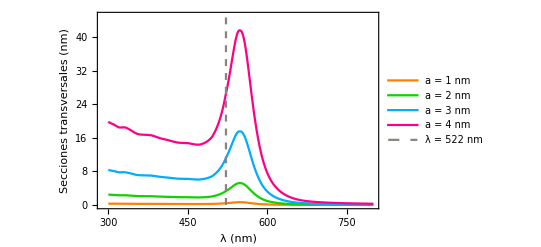

```mathematica
au1AR=ListLinePlot[{Style[qextAuAR,RGBColor[1,0.502,0]],Style[qextAu1AR,RGBColor[0.071,0.82,0]],Style[qextAu2AR,RGBColor[0,0.678,1]],Style[qextAu3AR,RGBColor[1,0,0.518]],Style[λtendencyAuAR,Dashed,RGBColor[0.541,0.518,0.498]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"a = 1 nm","a = 2 nm","a = 3 nm","a = 4 nm", "λ = 522 nm"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.65}]]
```

```mathematica
Export["AuAR.pdf",au1AR]
```

AuAR.pdf

#### Para ver las contribuciones cambiando a

```mathematica
qabsAucont=Table[{λ,Cabsexp[2,2,1,1.33,λ,nindexau1[λ]][[1]]},{λ,300,800}];
qscaAucont=Table[{λ,Cscaexp[2,2,1,1.33,λ,nindexau1[λ]][[1]]},{λ,300,800}];
qextAucont=Table[{λ,Cextexp[2,2,1,1.33,λ,nindexau1[λ]]},{λ,300,800}];
```

```mathematica
h vlight/500
```

2.4814

```mathematica
upperTicks4=Module[{labels,positions},labels={0.8,0.85,0.9,0.95,1,1.1,1.2,1.3,1.4,1.5,1.7,2,2.3,2.5,3.1,4};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={0.8,0.85,0.95,1.15,1.25,1.35,1.45,1.55,1.6,1.65,1.75,1.85,2.1,2.3,2.6,2.8};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

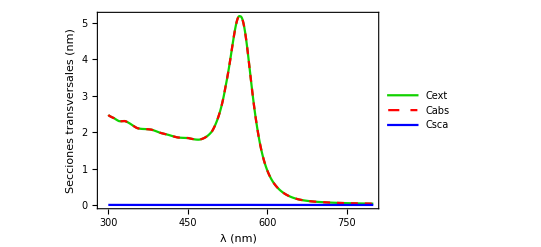

```mathematica
aucont=ListLinePlot[{Style[qextAucont,RGBColor[0.071,0.82,0]],Style[qabsAucont,Red,Dashed],Style[qscaAucont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
Export["AuContribuciones1.pdf",aucont]
```

AuContribuciones1.pdf

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en nm*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

```mathematica
nindexplata=Interpolation[plata];
```

#### Oblato

```mathematica
qabsAgc=Table[{λ,Cabsexp[2,2,1.33,λ,nindexplata[λ]][[1]]},{λ,300,550}];
qscaAgc=Table[{λ,Cscaexp[2,2,1,1.33,λ,nindexplata[λ]][[1]]},{λ,300,550}];
qextAgc=Table[{λ,Cextexp[2,2,1,1.33,λ,nindexplata[λ]]},{λ,300,550}];
qextAg1c=Table[{λ,Cextexp[2.5,2.5,1,1.33,λ,nindexplata[λ]]},{λ,300,550}];
qextAg2c=Table[{λ,Cextexp[3,3,1,1.33,λ,nindexplata[λ]]},{λ,300,550}];
qextAg3c=Table[{λ,Cextexp[3.5,3.5,1,1.33,λ,nindexplata[λ]]},{λ,300,550}];
qextAgEsferac=Table[{λ,Cextexp[4,4,4,1.33,λ,nindexplata[λ]]},{λ,300,550}];
λtendencyAgc=Table[{383,C},{C,0,480}];
```

```mathematica
h vlight/500
```

2.4814

```mathematica
upperTicksAg=Module[{labels,positions},labels={2.3,2.5,2.7,3,3.3,3.6,4};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAg=Module[{labels,positions,size},labels={2.3,2.6,2.9,3.2,3.5,3.7,4.2,4.5,5,5.7};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

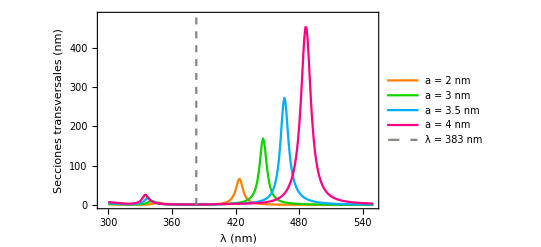

```mathematica
plata1c=ListLinePlot[{Style[qextAgc,RGBColor[1,0.502,0]],Style[qextAg1c,RGBColor[0.071,0.82,0]],Style[qextAg2c,RGBColor[0,0.678,1]],Style[qextAg3c,RGBColor[1,0,0.518]],Style[λtendencyAgc,Dashed,RGBColor[0.541,0.518,0.498]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"a = 2 nm","a = 3 nm","a = 3.5 nm","a = 4 nm", "λ = 383 nm"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.15,0.65}]]
```

```mathematica
Export["Agc.pdf",plata1c]
```

Agc.pdf

#### Misma razón de aspecto

```mathematica
qextAgAR=Table[{λ,Cextexp[1,1,0.5,1.33,λ,nindexplata[λ]]},{λ,300,500}];
qextAg1AR=Table[{λ,Cextexp[2,2,1,1.33,λ,nindexplata[λ]]},{λ,300,500}];
qextAg2AR=Table[{λ,Cextexp[3,3,1.5,1.33,λ,nindexplata[λ]]},{λ,300,500}];
qextAg3AR=Table[{λ,Cextexp[4,4,2,1.33,λ,nindexplata[λ]]},{λ,300,500}];
λtendencyAgAR=Table[{383,C},{C,0,550}];
```

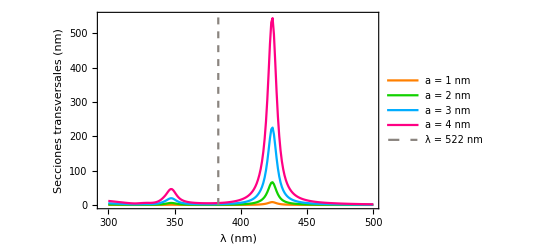

```mathematica
ag1AR=ListLinePlot[{Style[qextAgAR,RGBColor[1,0.502,0]],Style[qextAg1AR,RGBColor[0.071,0.82,0]],Style[qextAg2AR,RGBColor[0,0.678,1]],Style[qextAg3AR,RGBColor[1,0,0.518]],Style[λtendencyAgAR,Dashed,RGBColor[0.541,0.518,0.498]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"a = 1 nm","a = 2 nm","a = 3 nm","a = 4 nm", "λ = 522 nm"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.15,0.65}]]
```

```mathematica
Export["AgAR.pdf",ag1AR]
```

AgAR.pdf

#### Para ver las contribuciones cambiando a

```mathematica
qabsAgcont=Table[{λ,Cabsexp[15,15,1,1.33,λ,nindexplata[λ]][[1]]},{λ,750,950}];
qscaAgcont=Table[{λ,Cscaexp[15,15,1,1.33,λ,nindexplata[λ]][[1]]},{λ,750,950}];
qextAgcont=Table[{λ,Cextexp[15,15,1,1.33,λ,nindexplata[λ]]},{λ,750,950}];
```

```mathematica
h vlight/950
```

1.306

```mathematica
upperTicksAg=Module[{labels,positions},labels={1.3,1.34,1.37,1.4,1.45,1.5,1.55,1.6,1.65};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAg=Module[{labels,positions,size},labels={1.31,1.32,1.33,1.35,1.38,1.43,1.48,1.5,1.53,1.63};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

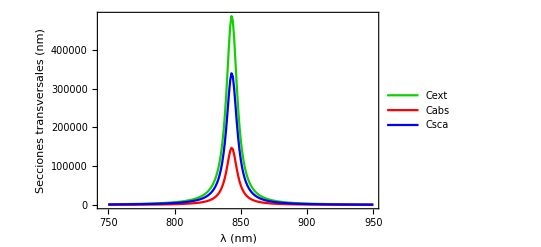

```mathematica
agcont=ListLinePlot[{Style[qextAgcont,RGBColor[0.071,0.82,0]],Style[qabsAgcont,Red],Style[qscaAgcont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
Export["AgContribuciones3.pdf",agcont]
```

AgContribuciones3.pdf

### Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]]*1000;(*λ en nm*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

```mathematica
nindexbismuto=Interpolation[bismuto];
```

```mathematica
10/(2*Pi*1.33)
```

1.19665

#### Oblato

```mathematica
qextBic=Table[{λ,Cextexp[1,1,0.5,1.33,λ,nindexbismuto[λ]]},{λ,10,900}];
qextBi1c=Table[{λ,Cextexp[1.25,1.25,0.5,1.33,λ,nindexbismuto[λ]]},{λ,10,900}];
qextBi2c=Table[{λ,Cextexp[1.5,1.5,0.5,1.33,λ,nindexbismuto[λ]]},{λ,10,900}];
qextBi3c=Table[{λ,Cextexp[1.75,1.75,0.5,1.33,λ,nindexbismuto[λ]]},{λ,0.1,900}];
qextBiEsferac=Table[{λ,Cextexp[1,1,1,1.33,λ,nindexbismuto[λ]]},{λ,0.1,900}];
λtendencyBic=Table[{383,C},{C,0,480}];
```

```mathematica
h vlight/800
```

1.55088

```mathematica
h vlight/20
```

62.035

```mathematica
upperTicksBi=Module[{labels,positions},labels={1.5,1.8,2,2.5,3,4,6,12.5,60};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorBi=Module[{labels,positions,size},labels={1.6,1.7,1.9,2.1,2.2,2.3,2.4,2.6,2.7,2.8,2.9,3.5,4.5,5,7,9,14,20,40};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

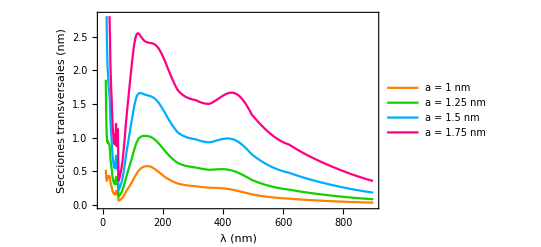

```mathematica
Bismuto1c=ListLinePlot[{Style[qextBic,RGBColor[1,0.502,0]],Style[qextBi1c,RGBColor[0.071,0.82,0]],Style[qextBi2c,RGBColor[0,0.678,1]],Style[qextBi3c,RGBColor[1,0,0.518]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorBi,upperTicksBi]}},PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"a = 1 nm","a = 1.25 nm","a = 1.5 nm","a = 1.75 nm", "λ = 383 nm"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.65}]]
```

```mathematica
Export["Bic.pdf",Bismuto1c]
```

Bic.pdf

#### Misma razón de aspecto

```mathematica
qextBiAR=Table[{λ,Cextexp[1,1,0.5,1.33,λ,nindexbismuto[λ]]},{λ,10,900}];
qextBi1AR=Table[{λ,Cextexp[1.25,1.25,0.625,1.33,λ,nindexbismuto[λ]]},{λ,10,900}];
qextBi2AR=Table[{λ,Cextexp[1.5,1.5,0.75,1.33,λ,nindexbismuto[λ]]},{λ,10,900}];
qextBi3AR=Table[{λ,Cextexp[1.75,1.75,0.875,1.33,λ,nindexbismuto[λ]]},{λ,0.1,900}];
```

```mathematica
1.75/2
```

0.875

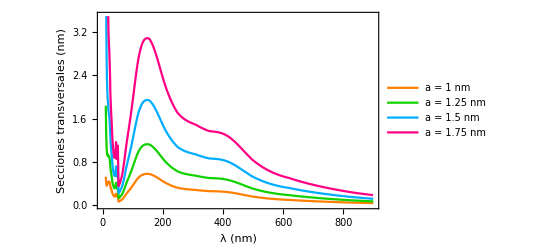

```mathematica
BismutoAR=ListLinePlot[{Style[qextBiAR,RGBColor[1,0.502,0]],Style[qextBi1AR,RGBColor[0.071,0.82,0]],Style[qextBi2AR,RGBColor[0,0.678,1]],Style[qextBi3AR,RGBColor[1,0,0.518]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorBi,upperTicksBi]}},PlotRange->{0,3.5},PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"a = 1 nm","a = 1.25 nm","a = 1.5 nm","a = 1.75 nm"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.65}]]
```

```mathematica
Export["BisAR.pdf",BismutoAR]
```

BisAR.pdf

#### Para ver las contribuciones cambiando a

```mathematica
qabsBicont=Table[{λ,Cabsexp[2,2,0.5,1.33,λ,nindexbismuto[λ]][[1]]},{λ,10,500}];
qscaBicont=Table[{λ,Cscaexp[2,2,0.5,1.33,λ,nindexbismuto[λ]][[1]]},{λ,10,500}];
qextBicont=Table[{λ,Cextexp[2,2,0.5,1.33,λ,nindexbismuto[λ]]},{λ,10,500}];
```

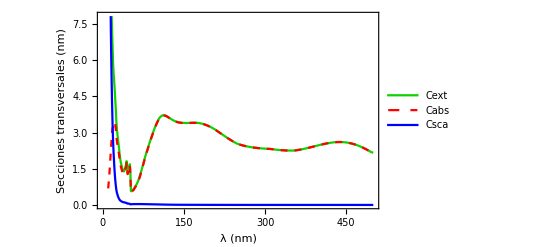

```mathematica
Bismutocont=ListLinePlot[{Style[qextBicont,RGBColor[0.071,0.82,0]],Style[qabsBicont,Red,Dashed],Style[qscaBicont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
Export["BiContribuciones1.pdf",Bismutocont]
```

BiContribuciones1.pdf

## Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]]*1000 ;(*λ en nm*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

```mathematica
nindexMgO=Interpolation[nmgo];
```

#### Oblato

```mathematica
qabsMgO=Table[{λ,Cabsexp[30,30,18,1.33,λ,nindexMgO[λ]][[1]]},{λ,360,1600}];
qscaMgO=Table[{λ,Cscaexp[30,30,18,1.33,λ,nindexMgO[λ]][[1]]},{λ,360,1600}];
qextMgO=Table[{λ,Cextexp[30,30,18,1.33,λ,nindexMgO[λ]]},{λ,360,1600}];
qextMgOx=Table[{λ,Cextexpx[30,30,18,1.33,λ,nindexMgO[λ]]},{λ,360,1600}];
qextMgOz=Table[{λ,Cextexpz[30,30,18,1.33,λ,nindexMgO[λ]]},{λ,360,1600}];
```

```mathematica
upperTicksMgO=Module[{labels,positions},labels={0.9,1,1.2,1.5,2,3};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorMgO=Module[{labels,positions,size},labels={1.1,1.3,1.4,1.7,1.9,2.3,2.6,2.9};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

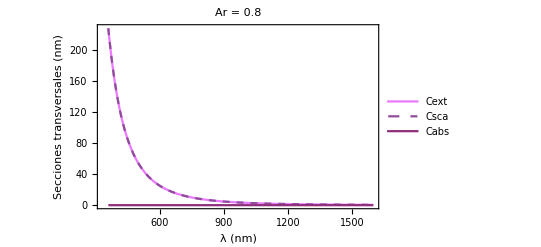

```mathematica
MgO1=ListLinePlot[{Style[qextMgO,RGBColor[0.922,0.475,1]],Style[qscaMgO,RGBColor[0.557,0.298,0.6],Dashed],Style[qabsMgO,RGBColor[0.561,0.18,0.475]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMgO,upperTicksMinorMgO]}},PlotRange->All,PlotLabel->Style["Ar = 0.8",FontFamily->"Times",18],PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Csca","Cabs"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.85,0.7}]]
```

```mathematica
Export["MgOAr0.8c18a30.pdf",MgO1]
```

MgOAr0.8c18a30.pdf

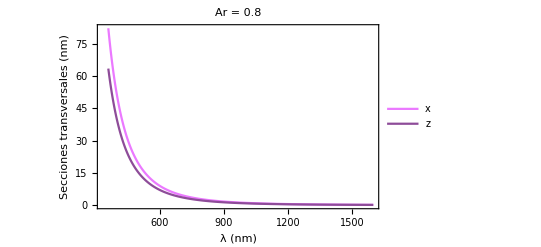

```mathematica
MgO1=ListLinePlot[{Style[qextMgOx,RGBColor[0.922,0.475,1]],Style[qextMgOz,RGBColor[0.557,0.298,0.6]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMgO,upperTicksMinorMgO]}},PlotRange->All,PlotLabel->Style["Ar = 0.8",FontFamily->"Times",18],PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"x","z"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.85,0.7}]]
```

```mathematica
Export["MgOxzAr0.6c18a30.pdf",MgO1]
```

MgOxzAr0.6c18a30.pdf

## Eritrocitos

```mathematica
RBCreal=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\NRealRBC.csv"];
RBCimag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\NImagRBC.csv"];
```

```mathematica
λRBC=RBCreal[[All,1]];
nRBC=RBCreal[[All,2]];
kRBC=RBCimag[[All,2]];
nindRBC=nRBC+ I kRBC;
RBC=Transpose[{λRBC,nindRBC}];
```

```mathematica
nindexRBC=Interpolation[RBC];
```

```mathematica
qabsRBC=Table[{λ,Cabsexp[20,20,12,1.33,λ,nindexRBC[λ]][[1]]},{λ,400,600}];
qscaRBC=Table[{λ,Cscaexp[20,20,12,1.33,λ,nindexRBC[λ]][[1]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexp[20,20,12,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexpx[6,6,2,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexpz[6,6,2,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
```

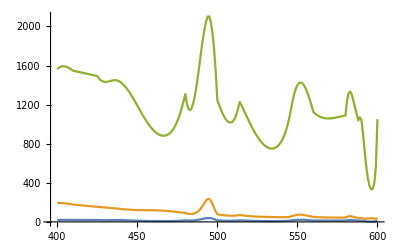

```mathematica
ListLinePlot[{qextRBC,qscaRBC,qabsRBC}]
```